# 数据处理

```mathematica
data=Import[NotebookDirectory[]<>"..\\..\\data\\2020_Problem_D_DATA\\fullevents.csv"];
```

```mathematica
object=Transpose[data][[{3,4,8}]];
```

```mathematica
myteam=Drop[Thread[Table[object[[i]],{i,1,3}]],1];
```

# 函数

```mathematica
function1[alpha_]:=Cases[alpha,{x_,y_,z_}/;(If[x=="",False,StringSplit[x,"_"][[1]]=="Huskies"]||If[y=="",False,StringSplit[y,"_"][[1]]=="Huskies"])&&z=="Simple pass"]
```

```mathematica
function2[beta_]:=Cases[beta,{x_,y_,z_}/;(If[x=="",False,StringSplit[x,"_"][[1]]=="Huskies"]||If[y=="",False,StringSplit[y,"_"][[1]]=="Huskies"])]
```

```mathematica
Length@function1[myteam]
```

10172

```mathematica
Length@function2[myteam]
```

28217

```mathematica
Length@function1[myteam]/Length@function2[myteam]//N
```

0.360492

```mathematica
functionnew1[alpha_,member_]:=Cases[alpha,{x_,y_,z_}/;(If[x=="",False,x==member]||If[y=="",False,y==member])&&z=="Simple pass"]
```

```mathematica
functionnew2[alpha_,member_]:=Cases[alpha,{x_,y_,z_}/;If[x=="",False,x==member]||If[y=="",False,y==member]]
```

```mathematica
Length@functionnew1[myteam,"Huskies_D1"]/Length@functionnew2[myteam,"Huskies_D1"]
```

277/530

```mathematica
functionnew2[myteam,"Huskies_D1"]
```

{{Huskies_D1,Huskies_F1,Head pass},{Huskies_D1,,High pass},{Huskies_D1,Huskies_F1,Head pass},{Huskies_D1,Huskies_G1,Simple pass},2642,{Huskies_D1,Huskies_M1,Simple pass},{Huskies_D1,,Ground defending duel},{Huskies_D1,,Ground defending duel},{Huskies_D1,,Air duel}}
 |  |  |  |

# 测试

```mathematica
fraction[gammar_,member_]:=Length@functionnew1[gammar,member]/Length@functionnew2[gammar,member]
```

```mathematica
fractionmyteam[member_]:=fraction[myteam,member]
```

```mathematica
fractionmyteam["Huskies_D1"]
```

277/530

# Member

```mathematica
allmember=Table["Huskies_"<>"F"<>ToString[i],{i,1,6}]~Join~Table["Huskies_"<>"M"<>ToString[i],{i,1,13}]~Join~
Table["Huskies_"<>"D"<>ToString[i],{i,1,10}]~Join~
Table["Huskies_"<>"G"<>ToString[i],{i,1,1}]
```

{Huskies_F1,Huskies_F2,Huskies_F3,Huskies_F4,Huskies_F5,Huskies_F6,Huskies_M1,Huskies_M2,Huskies_M3,Huskies_M4,Huskies_M5,Huskies_M6,Huskies_M7,Huskies_M8,Huskies_M9,Huskies_M10,Huskies_M11,Huskies_M12,Huskies_M13,Huskies_D1,Huskies_D2,Huskies_D3,Huskies_D4,Huskies_D5,Huskies_D6,Huskies_D7,Huskies_D8,Huskies_D9,Huskies_D10,Huskies_G1}

```mathematica
a=fractionmyteam/@allmember
```

{74/327,1678/2861,120/251,303/1106,296/903,424/1053,2239/3566,141/236,513/821,982/1913,81/152,992/2101,40/61,339/713,277/642,79/192,59/104,4/11,127/235,277/530,954/1759,1169/2102,1148/1957,1075/2228,193/423,761/1777,499/1103,93/145,62/133,204/703}

```mathematica
a//N
```

{0.2263,0.586508,0.478088,0.27396,0.327796,0.402659,0.627874,0.597458,0.624848,0.51333,0.532895,0.472156,0.655738,0.475456,0.431464,0.411458,0.567308,0.363636,0.540426,0.522642,0.542354,0.556137,0.586612,0.482496,0.456265,0.42825,0.452403,0.641379,0.466165,0.290185}

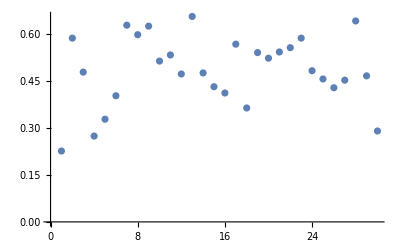

```mathematica
ListPlot[%117]
```